```mathematica
f=Get["/home/carla/GDC/CONF/DLB/DLB_F.txt"]
baa=Get["/home/carla/GDC/CONF/DLB/DLB_F_APP.txt"]
```

{{0,1},{0.5,1},{1,1},{1.5,1},{2,0.682016},{2.5,0.69382},{3,0.921345},{3.5,0.917488},{4,0.890847},{4.5,0.901714},{5,0.899351},{5.5,0.912511},{6,0.940507},{6.5,0.804199},{7,0.951201},{7.5,0.951024},{8,1}}

{{0,0.000341491},{0.5,0.000436062},{1,0.000436062},{1.5,0.000277936},{2,128.896},{2.5,123.248},{3,6.38482},{3.5,6.7113},{4,7.7902},{4.5,8.26685},{5,8.68802},{5.5,10.1536},{6,1.11893},{6.5,13.3918},{7,0.750518},{7.5,0.75331},{8,0.000435964}}

```mathematica
diffF=Table[{f[[i,1]],(f[[i+1,2]]-f[[i,2]])},{i,1,16,1}][[4;;-2]]
diffbaa=Table[{baa[[i,1]],(baa[[i+1,2]]-baa[[i,2]])},{i,1,16,1}][[4;;-2]]
```

{{1.5,-0.317984},{2,0.0118036},{2.5,0.227525},{3,-0.00385715},{3.5,-0.0266407},{4,0.0108673},{4.5,-0.00236302},{5,0.0131602},{5.5,0.0279953},{6,-0.136307},{6.5,0.147001},{7,-0.000177199}}

{{1.5,128.896},{2,-5.64802},{2.5,-116.863},{3,0.326486},{3.5,1.07889},{4,0.476649},{4.5,0.421174},{5,1.46554},{5.5,-9.03463},{6,12.2728},{6.5,-12.6412},{7,0.00279118}}

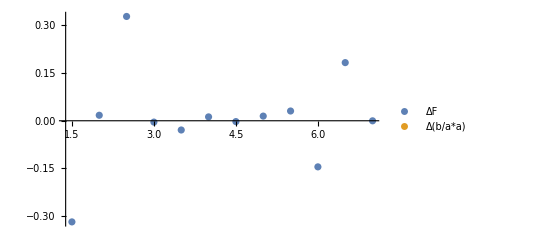

```mathematica
ListPlot[{diffF,diffab}, PlotLegends->{"ΔF","Δ(b/a*a)" }, PlotRange->All]
```

```mathematica
deltaLA[a_,b_]:=Module[{delta},
delta=(2*b)/(a*a +2a*b-4a*a*b);
Return[delta];];
deltaLB[a_,b_]:=Module[{delta},
delta=(-2*a+2*a*a)/(a*a +2a*b-4a*a*b);
Return[delta];];
```

```mathematica
a1=0.00146843;
a2=0.00645161;
b1=0.000266;
b2=0.000266;
L1=0.69382;
L2=0.921345;
```

```mathematica
deltaL=L2-L1
```

0.227525

```mathematica
(a2-a1)*deltaLA[a1,b1]
```

0.903194